```mathematica
FullSimplify[RSolve[{1/r[n] == 1/R+1/(2R+r[n-1]),r[1]==R},r[n],n]]
```

{{r[n]→(-1+√3+(2 √3 (2-√3)^n)/(-(2-√3)^n+(2+√3)^n)) R}}

```mathematica
a=R
b=3a^2
c=1
d=3a
```

R

3 R^2

1

3 R

```mathematica
a*d-b*c
```

0

```mathematica
(d-a)^2+4*b*c
```

16 R^2

```mathematica
Solve[1/r[n] == 1/R+1/(2R+r[n-1]),r[n]]
```

{{r[n]→(R (2 R+r[-1+n]))/(3 R+r[-1+n])}}

```mathematica
Limit[(-1+√3+(2 √3 (2-√3)^n)/(-(2-√3)^n+(2+√3)^n)) R,n-> ∞]
```

(-1+√3) R

```mathematica
Solve[0 == r^2+2R r - 2R^2,r]
```

{{r→-R-√3 R},{r→-R+√3 R}}

```mathematica
(-1+√3+(2 √3 (2-√3)^n)/(-(2-√3)^n+(2+√3)^n))
```

-1+√3+(2 √3 (2-√3)^n)/(-(2-√3)^n+(2+√3)^n)

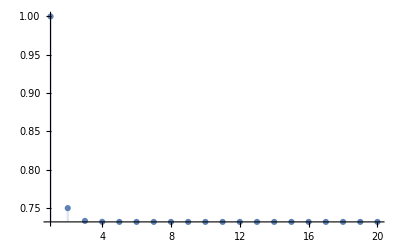

```mathematica
DiscretePlot[-1+√3+(2 √3 (2-√3)^n)/(-(2-√3)^n+(2+√3)^n),{n,1,20},PlotRange->All]
```